# FP Comparison

## Preliminaries

```mathematica
maindir=SetDirectory[NotebookDirectory[]]
nbf=NotebookFileName[]
```

/storage/disqs/CCxD/Analysis_SS

/storage/disqs/CCxD/Analysis_SS/FPComparison.nb

### Setting Parameters

```mathematica
matrix =1;
configs = 1000000000;
importrangeid = Table[i,{i,1,10}];
importrangerg = Table[i,{i,0,10}];
zrange = 50;
cropamt=8;
project="CC2D";
```

## Importing Data

```mathematica
datadir=maindir<>"/../"<>project<>"/data/";
SetDirectory[datadir];
```

```mathematica
zimport = Table[Flatten[Import[ToString[datadir]<>ToString[matrix]<>"-RG-"<>ToString[configs]<>"-"<>ToString[i]<>"/dists/"<>ToString[j]<>"/"<>ToString[matrix]<>"-z"<>"-"<>ToString[configs]<>"-averaged-symmetrized"<>".txt","Data"]],{i,importrangeid},{j,importrangerg}];
timport = Table[Flatten[Import[ToString[datadir]<>ToString[matrix]<>"-RG-"<>ToString[configs]<>"-"<>ToString[i]<>"/dists/"<>ToString[j]<>"/"<>ToString[matrix]<>"-t"<>"-"<>ToString[configs]<>"-averaged"<>".txt","Data"]],{i,importrangeid},{j,importrangerg}];
gimport = Table[Flatten[Import[ToString[datadir]<>ToString[matrix]<>"-RG-"<>ToString[configs]<>"-"<>ToString[i]<>"/dists/"<>ToString[j]<>"/"<>ToString[matrix]<>"-g"<>"-"<>ToString[configs]<>"-averaged"<>".txt","Data"]],{i,importrangeid},{j,importrangerg}];
croppedzimport = Table[Take[Flatten[Import[ToString[datadir]<>ToString[matrix]<>"-RG-"<>ToString[configs]<>"-"<>ToString[i]<>"/dists/"<>ToString[j]<>"/"<>ToString[matrix]<>"-z"<>"-"<>ToString[configs]<>"-averaged-symmetrized"<>".txt","Data"]],{1000* (zrange -cropamt),1000*(zrange+cropamt)}],{i,importrangeid},{j,importrangerg}];
```

```mathematica
ttotal = Table[Total[timport[[i]][[j]]],{i,importrangeid},{j,1,Length[importrangerg]}];
gtotal = Table[Total[gimport[[i]][[j]]],{i,importrangeid},{j,1,Length[importrangerg]}];
ztotal = Table[Total[zimport[[i]][[j]]],{i,importrangeid},{j,1,Length[importrangerg]}];
tnormalized = Table[{k/1000,1000*timport[[i]][[j]][[k]]/ttotal[[i]][[j]]},{i,importrangeid},{j,1,Length[importrangerg]},{k,1,Length[timport[[1]][[1]]]}];
gnormalized = Table[{k/1000,1000*gimport[[i]][[j]][[k]]/gtotal[[i]][[j]]},{i,importrangeid},{j,1,Length[importrangerg]},{k,1,Length[gimport[[1]][[1]]]}];
znormalized = Table[{(k/1000)-(zrange + 0.0005),1000*zimport[[i]][[j]][[k]]/ztotal[[i]][[j]]},{i,importrangeid},{j,1,Length[importrangerg]},{k,1,Length[zimport[[1]][[1]]]}];
zcroppednormalized = Table[Take[znormalized[[i]][[j]],{1000* (zrange -cropamt),1000*(zrange+cropamt)}],{i,importrangeid},{j,1,Length[importrangerg]}];
```

```mathematica
ex = Table[znormalized[[i]][[j]][[k]][[1]]*znormalized[[i]][[j]][[k]][[2]]*(1/1000),{i,importrangeid},{j,1,Length[importrangerg]},{k,1,Length[znormalized[[1]][[1]]]}];
exsquared = Table[znormalized[[i]][[j]][[k]][[1]]^2*znormalized[[i]][[j]][[k]][[2]]*(1/1000),{i,importrangeid},{j,1,Length[importrangerg]},{k,1,Length[znormalized[[1]][[1]]]}];
var = Table[Total[exsquared[[i]][[j]]]-Total[ex[[i]][[j]]]^2,{i,importrangeid},{j,1,Length[importrangerg]}];
stdev = Table[Sqrt[var[[i]][[j]]],{i,importrangeid},{j,1,Length[importrangerg]}];
stdevav = Table[Total[Transpose[stdev][[i]]],{i,1,Length[importrangerg]}]
difference = Table[Abs[znormalized[[i]][[j+1]][[k]][[2]]-znormalized[[i]][[j]][[k]][[2]]]^2,{i,importrangeid},{j,1,Length[znormalized[[1]]]-1},{k,1,Length[znormalized[[1]][[1]]]}]
difftotal = Table[Total[difference[[i]][[j]]],{i,importrangeid},{j,1,Length[znormalized[[1]]]-1}]
delta = Table[Sqrt[(1/1000)*(difftotal[[i]][[j]])],{i,importrangeid},{j,1,Length[znormalized[[1]]]-1}];
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}
 |  |  |  |

{{1.30208,0.42939,0.103351,0.0205781,0.00431736,0.00149088,0.00104402,0.00100345,0.00100458,0.000987358},{1.30052,0.431044,0.103523,0.0203736,0.00434497,0.00159668,0.00109847,0.000984653,0.000969557,0.00101788},{1.30128,0.431723,0.103509,0.020244,0.00437426,0.00151999,0.00121026,0.0011336,0.00102891,0.000947323},{1.30206,0.430917,0.102659,0.020466,0.00441151,0.00149992,0.00102639,0.00100094,0.00110807,0.00109718},{1.30279,0.430939,0.102948,0.0205293,0.00437314,0.00158492,0.00112225,0.0010423,0.000982798,0.000960241},{1.30276,0.431459,0.102991,0.0200514,0.0042574,0.00158499,0.00108228,0.00102553,0.0010149,0.00101534},{1.30383,0.431108,0.102235,0.020398,0.00429988,0.00157759,0.00110355,0.000997288,0.000982975,0.000963947},{1.30205,0.429939,0.102889,0.0206154,0.00431384,0.00154034,0.00110114,0.00101695,0.00112763,0.00111104},{1.3013,0.431158,0.103497,0.0202464,0.0043282,0.00154186,0.00109228,0.000953797,0.00102324,0.000982625},{1.30265,0.43042,0.102565,0.0205937,0.00432949,0.00152319,0.00108444,0.00105891,0.00101639,0.00102577}}

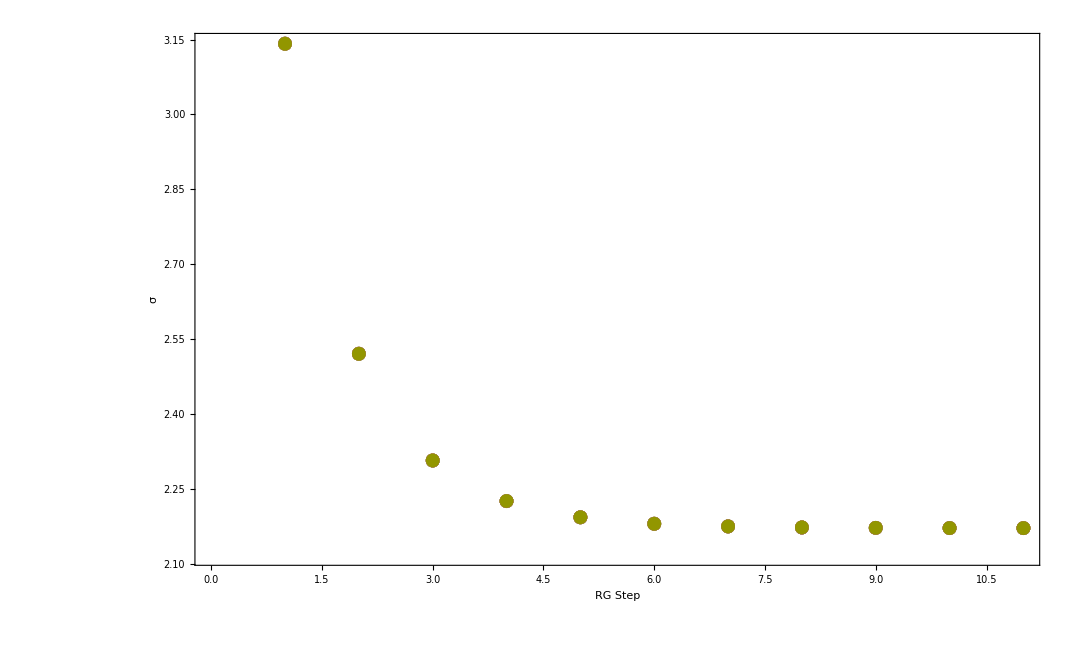

```mathematica
ListPlot[stdev, Frame->True,  LabelStyle->{FontSize->24},FrameLabel->{"RG Step","σ"}]
```

{{3.14148,2.5207,2.30717,2.22571,2.19309,2.18017,2.175,2.17278,2.17193,2.17158,2.17156},{3.14138,2.52066,2.30696,2.22551,2.19322,2.18013,2.17488,2.17278,2.17199,2.17171,2.17152},{3.14155,2.52061,2.30683,2.22544,2.19309,2.18007,2.17494,2.17269,2.17186,2.17161,2.17154},{3.14154,2.52064,2.30691,2.22571,2.19323,2.1801,2.175,2.17298,2.17195,2.17158,2.17158},{3.14162,2.52058,2.30695,2.22555,2.19312,2.18005,2.17488,2.17266,2.17192,2.17134,2.17143},{3.14159,2.52043,2.30661,2.22533,2.19314,2.18024,2.17493,2.17275,2.17187,2.17149,2.17137},{3.14159,2.52044,2.30675,2.2256,2.19311,2.1802,2.17489,2.17279,2.17198,2.17159,2.17136},{3.14155,2.52064,2.30707,2.22555,2.19313,2.18015,2.17488,2.17276,2.17195,2.17157,2.1715},{3.14165,2.52074,2.30699,2.22547,2.19308,2.18018,2.17481,2.17261,2.1719,2.1716,2.17137},{3.14152,2.52056,2.30691,2.22568,2.1932,2.18011,2.17487,2.1729,2.17203,2.17155,2.17141}}

{3.14155,2.5206,2.30691,2.22556,2.19314,2.18014,2.17491,2.17277,2.17194,2.17156,2.17146}

{{0.0000694555,-0.0000977642,-0.000250686,-0.000152126,0.0000499058,-0.0000343394,-0.0000898268,-0.0000104206,0.0000111426,-0.0000186097,-0.0000915573},{0.000167418,-0.0000642609,-0.0000492975,0.0000494284,-0.0000833217,6.21707×10^-6,0.0000307474,-0.0000124459,-0.0000533666,-0.000147976,-0.0000545055},{-2.9483×10^-6,-0.0000136388,0.0000826051,0.000114986,0.0000531567,0.0000712024,-0.0000324678,0.0000823455,0.0000800733,-0.0000446206,-0.0000727746},{3.16639×10^-6,-0.0000389113,5.61981×10^-6,-0.000157169,-0.0000851898,0.0000363721,-0.0000911719,-0.000207379,-0.0000137902,-0.000017098,-0.000120955},{-0.0000696483,0.0000203182,-0.0000324124,7.49513×10^-6,0.0000186641,0.0000895554,0.0000291372,0.000108996,0.0000178207,0.000218158,0.0000307671},{-0.0000483722,0.000171408,0.000302687,0.000228521,2.94637×10^-6,-0.0000952849,-0.0000270125,0.0000231998,0.0000686207,0.0000724156,0.0000952601},{-0.0000406287,0.000160264,0.000168822,-0.000048608,0.0000314033,-0.0000589878,0.0000217135,-0.0000161689,-0.0000404923,-0.0000317136,0.000102675},{-5.22969×10^-6,-0.0000403419,-0.000154342,6.8602×10^-7,0.0000101969,-8.39741×10^-6,0.0000239798,0.0000125467,-0.0000136891,-6.54286×10^-6,-0.0000348537},{-0.000100847,-0.000141597,-0.0000744224,0.0000824285,0.0000583835,-0.0000398809,0.000093906,0.000155064,0.0000411664,-0.0000371288,0.0000966918},{0.0000276344,0.0000445247,1.42518×10^-6,-0.000125641,-0.0000561452,0.0000335435,0.0000409952,-0.000135738,-0.0000974855,0.0000131159,0.0000492522}}

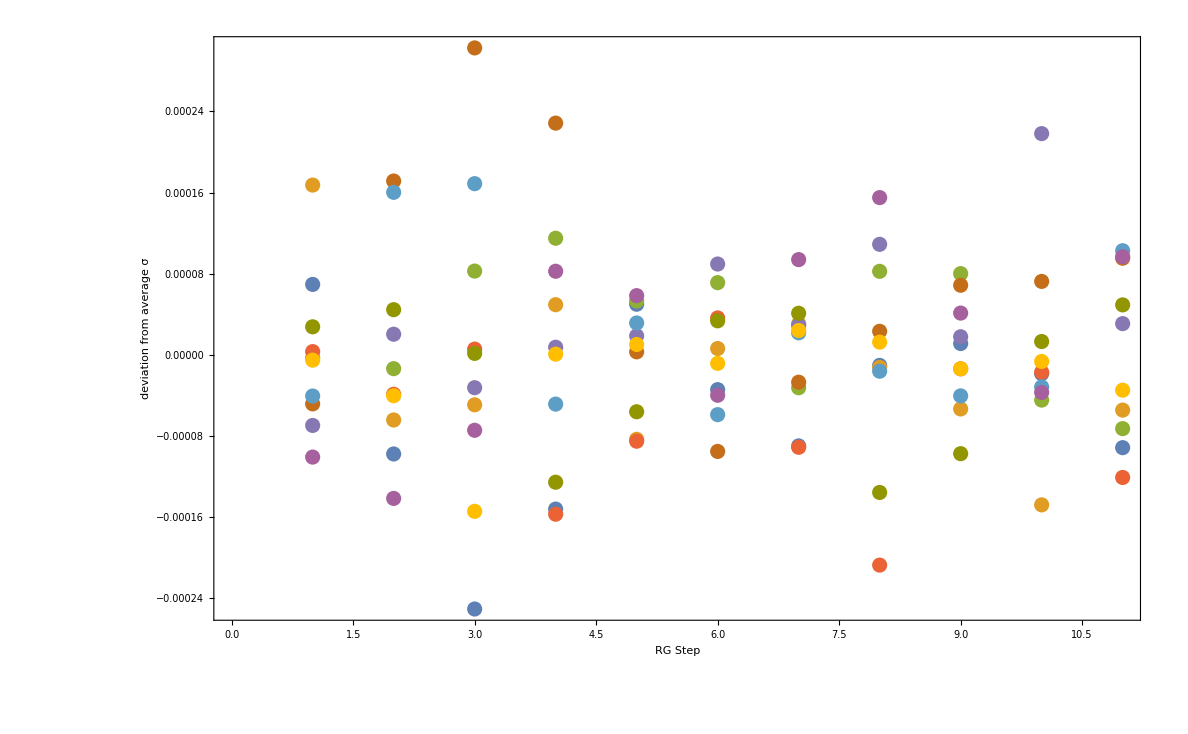

```mathematica
stdev
stdevav = Table[Total[Transpose[stdev][[i]]]/Length[importrangeid],{i,1,Length[importrangerg]}]
stdevdeviation = Table[stdevav[[j]]-stdev[[i]][[j]],{i,importrangeid},{j,1,Length[importrangerg]}]
ListPlot[stdevdeviation, Frame->True, LabelStyle->{FontSize->24},FrameLabel->{"RG Step","deviation from average σ"}]
```

```mathematica
delta
```

{{0.0360844,0.0207217,0.0101662,0.00453631,0.00207783,0.00122101,0.00102177,0.00100172,0.00100229,0.000993659},{0.0360627,0.0207616,0.0101746,0.00451371,0.00208446,0.0012636,0.00104808,0.000992297,0.000984661,0.0010089},{0.0360733,0.0207779,0.010174,0.00449934,0.00209147,0.00123288,0.00110012,0.00106471,0.00101435,0.000973305},{0.0360841,0.0207585,0.0101321,0.00452394,0.00210036,0.00122471,0.00101311,0.00100047,0.00105265,0.00104746},{0.0360941,0.0207591,0.0101463,0.00453092,0.00209121,0.00125894,0.00105936,0.00102093,0.000991362,0.000979919},{0.0360938,0.0207716,0.0101484,0.00447788,0.00206335,0.00125896,0.00104032,0.00101268,0.00100742,0.00100764},{0.0361086,0.0207631,0.0101111,0.00451642,0.00207362,0.00125602,0.0010505,0.000998643,0.000991451,0.000981808},{0.0360839,0.020735,0.0101434,0.00454042,0.00207698,0.00124111,0.00104935,0.00100844,0.0010619,0.00105406},{0.0360735,0.0207644,0.0101733,0.0044996,0.00208043,0.00124172,0.00104512,0.000976625,0.00101155,0.000991275},{0.0360922,0.0207466,0.0101275,0.00453803,0.00208074,0.00123418,0.00104136,0.00102904,0.00100816,0.0010128}}